```mathematica
imgRes= {n,n}/.n->64; η=1/2;
1-ExampleData[{"TestImage", "ResolutionChart"}];
ImagePad[%, (1-η)/(2η)*{imgRes, imgRes}];
img = ImageData@ImageResize[%, imgRes];
Dimensions@img
{img//Image[#,ImageSize->Medium]&}
```

{64,64}

{-Graphics-}

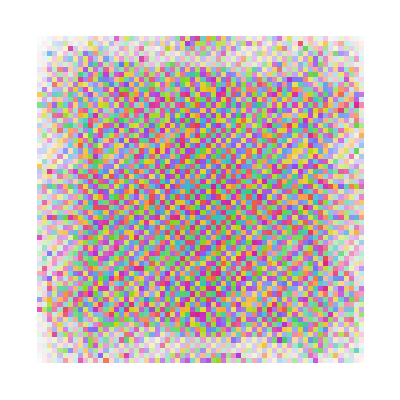
{-Graphics-,-Graphics-}

```mathematica
imgF = Fourier[img];
(*x =Round[256/2*0.8];
imgF[[128-x;;128+x,128-x;;128+x]] = 0 ;
*)
{imgF// ComplexArrayPlot
,imageFR =Abs@InverseFourier[imgF]//Image}
```

```mathematica
δ[u_, v_, ϕ_]:= SparseArray[{u,v}->ⅇ^(ⅈ*ϕ), imgRes];
P[u_, v_, ϕ_]:=1/2(1+Re[InverseFourier[δ[u, v, ϕ]]])//RotateRight[#, {8, 0}]&;
fourFourier[u_, v_] :=(P[u,v,π]-P[u,v,0]) + ⅈ(P[u,v,(3π)/2]-P[u,v,π/2]);
fftShift[data_]:=RotateRight[data,Floor[(Dimensions@data-1)/2]];
```

```mathematica
(* Run reconstruction algorithm *)
imgF=Table[Total[fourFourier[u,v]*img, 2], {u,imgRes[[1]]}, {v,imgRes[[2]]}];//AbsoluteTiming
Abs@fftShift@imgF//Image;
Abs@InverseFourier@fftShift@imgF//Image;
{%%,%}
```

{3.44205,Null}

{-Graphics-,-Graphics-}

```mathematica
ClearSystemCache[];
δ[5,5,0];//AbsoluteTiming
P[5,5,0];//AbsoluteTiming
Table[Total[fourFourier[u,v]*img, 2], {u,1}, {v,1}];//AbsoluteTiming
```

{0.000138,Null}

{0.000477,Null}

{0.001354,Null}

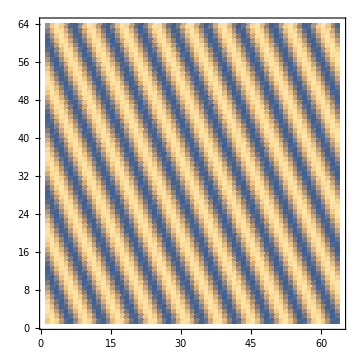

```mathematica
P[5,10,3π/2]//ListDensityPlot[#,ImageSize->Medium]&
```